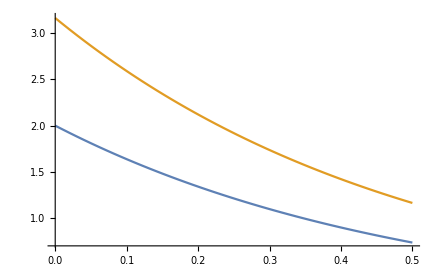

```mathematica
f[t_]:= a*Exp[-a*t];
f2[t_] := a/(1-Exp[-a*tm])*Exp[-a*t];
a= 2;
tm = 0.5;
Plot[{f[t], f2[t]}, {t,0,tm}]
```

```mathematica
Integrate[f2[x], {x,0,tm}]
```

```mathematica
f2[1]
```

0.428195

```mathematica
Integrate[f[x], {x,-1,1}]
```

$Aborted

```mathematica
NIntegrate[f[x],{x,-1,1}, AccuracyGoal->10]
```

0.0000527847

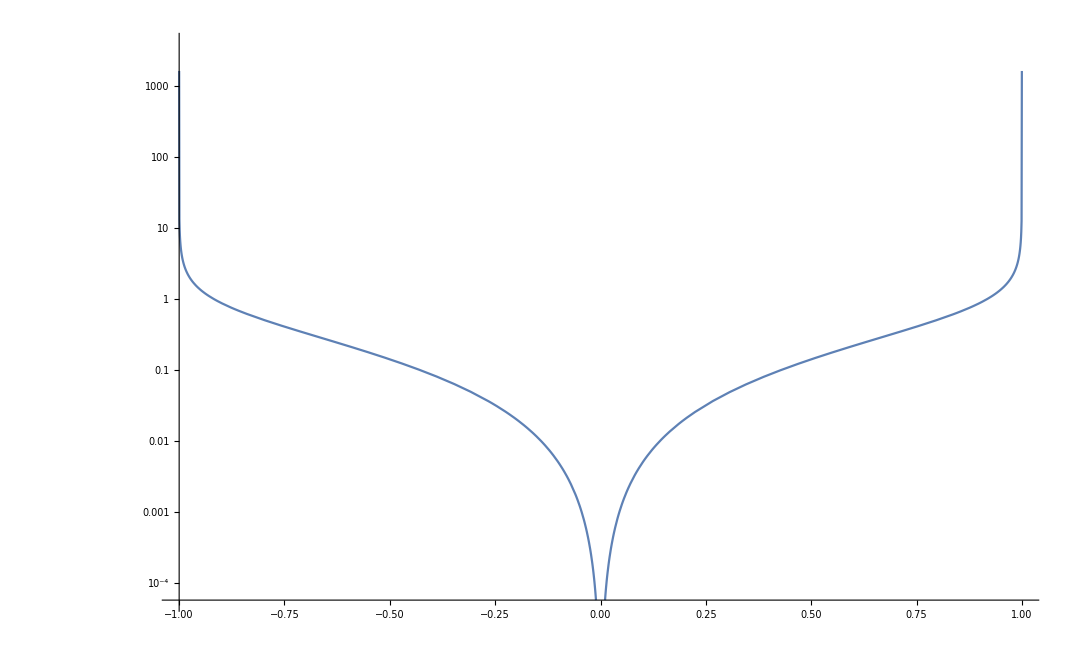

```mathematica
LogPlot[f[x], {x,-1,1}]
```